# ESF First Mathematica Notebook

### Define a function

```mathematica
nNewPop[origPop_, rate_, carCap_] := origPop + origPop * (rate * (1 - origPop/carCap))
```

### Generate Interactive plot that manipulates reproduction rate

```mathematica
Manipulate[ListLinePlot[NestList[nNewPop[#, rdr, 1200]&,1000, 100],PlotRange -> {All, {0, 1700}}],{{rdr, 0.2}, 0,3,Appearance->"Labeled"}]
```

### Plot the differences between two simulations

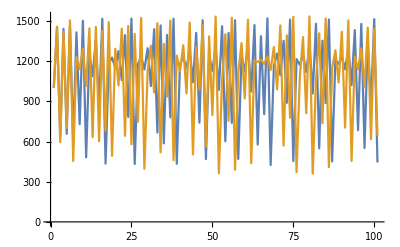

```mathematica
sim1 = NestList[nNewPop[#, 2.7, 1200]&,1000, 100];
sim2 = NestList[nNewPop[#, 2.75, 1200]&,1000, 100];
ListLinePlot[{sim1,sim2}]
```

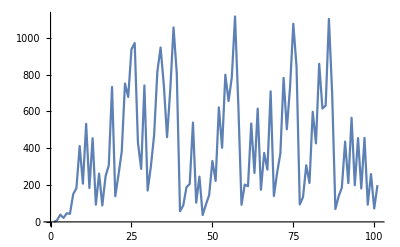

```mathematica
ListLinePlot[Abs[{sim1-sim2}]]
```

#### Dynamically plot the difference between two simulations that vary in rate

```mathematica
Manipulate[ListLinePlot[Abs[{NestList[nNewPop[#, rdr1, 1200]&,1000, 100] - NestList[nNewPop[#, rdr2, 1200]&,1000, 100]}],PlotRange -> {All, {0, 1700}}],{{rdr1, 1.9}, 0,3,Appearance->"Labeled"},{{rdr2, 2.1}, 0,3,Appearance->"Labeled"}]
```